```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/akapiisp/Documents/research/Self-similar approximations

Maybe I should use the Borel self similar summation technique discussed in 2505.12119 to get real solutions

### With pressure Nsolve:

```mathematica
Iorder = 1;
Ttable = Table[i,{i,80,300,2}];
μtable = Table[i/j,{j,80,300,2},{i,0,800,800/Length[Ttable]}];
Pfunc[T_] =  Interpolation[Pdata,InterpolationOrder->Iorder][T];
chi2func[T_] = Interpolation[chi2,InterpolationOrder->Iorder][T];
chi4func[T_] = Interpolation[chi4,InterpolationOrder->Iorder][T];
chi6func[T_] = Interpolation[chi6,InterpolationOrder->Iorder][T];
chi8func[T_] = Interpolation[chi8,InterpolationOrder->Iorder][T];
chi10func[T_] = Interpolation[chi10,InterpolationOrder->Iorder][T];

Plist = Pfunc[Ttable];
chi2list = chi2func[Ttable];
chi4list = chi4func[Ttable];
chi6list = chi6func[Ttable];
chi8list = chi8func[Ttable];
chi10list = chi10func[Ttable];
```

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

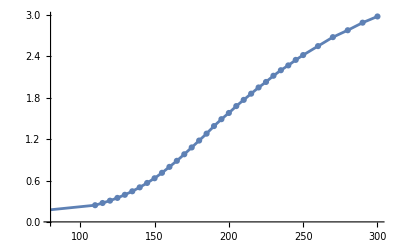

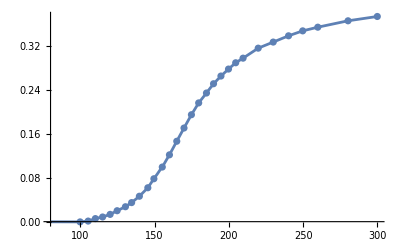

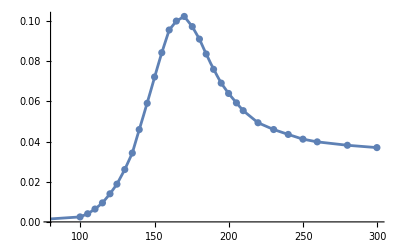

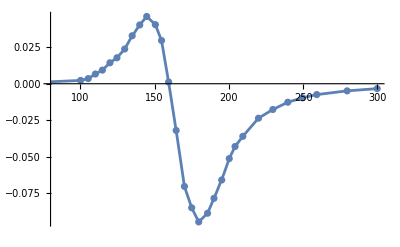

```mathematica
Show[{Plot[Pfunc[T],{T,80,300}],ListPlot[Pdata]}]
Show[{Plot[chi2func[T],{T,80,300}],ListPlot[chi2]}]
Show[{Plot[chi4func[T],{T,80,300}],ListPlot[chi4]}]
Show[{Plot[chi6func[T],{T,80,300}],ListPlot[chi6]}]
```

```mathematica
P={};
For[i=1,i≤Length[Ttable],i++,coeffs={1,chi2list⟦i⟧/(2! Plist⟦i⟧),chi4list⟦i⟧/(4! Plist⟦i⟧),chi6list⟦i⟧/(6! Plist⟦i⟧),chi8list⟦i⟧/(8! Plist⟦i⟧),chi10list⟦i⟧/(10! Plist⟦i⟧)};x=Symbol["x"];k=Length[coeffs]-1;m=(k+1)/2;At=Table[A[j],{j,1,m}];
nt=Table[n[j],{j,1,m}];

(*---Construct factor approximant---*)
factorApprox=Times@@Table[(1+At[[i]] x)^nt[[i]],{i,1,m}];

(*---Expand and collect series---*)
seriesApprox=Normal[Series[factorApprox,{x,0,k}]];

(*---Create equations by matching coefficients---*)
equations=Table[Coefficient[seriesApprox,x,j-1]==coeffs[[j]],{j,1,k+1}];
(*Should probably also have AppendTo[equations,Total[nt]=2]*)

(*---Solve for parameters---*)
(*Solve over reals, maybe the exponents could be complex for DSI*)
solutions=NSolve[equations,Join[At,nt]];

(*---Factor approximant with solved parameters---*)
factorApproximant=Plist[[i]]*factorApprox/. solutions /. x-> μ^2;
aux ={{factorApproximant}};
For[j=1,j≤Length[μtable⟦i⟧],j++,
AppendTo[aux,{μtable⟦i,j⟧ Ttable⟦i⟧,Ttable⟦i⟧,factorApproximant/.μ->μtable⟦i,j⟧}];];

AppendTo[P,aux];
Print[i];Export["withpressureNsolve.mx",P]];
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(19857 A[1])/30458+(20993 A[2])/30458-(27178 A[3])/45687-(71297 n[1])/91374-(173881 n[2])/182748+(11342 n[3])/15229 == 1.

1

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(19857 A[1])/30458+(20993 A[2])/30458-(27178 A[3])/45687-(71297 n[1])/91374-(173881 n[2])/182748+(11342 n[3])/15229 == 1.

2

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(19857 A[1])/30458+(20993 A[2])/30458-(27178 A[3])/45687-(71297 n[1])/91374-(173881 n[2])/182748+(11342 n[3])/15229 == 1.

General::stop: Further output of NSolve::infsolns will be suppressed during this calculation.

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

```mathematica
P = Import["withpressureNsolve.mx"];
results = {#[[1]],#[[2]],Re[#[[3,1]]]} &/@Flatten[P[[;;,2;;]],1];
```

```mathematica
ListPointPlot3D[results[[;;]],AxesLabel->{"μ","T","P"},PlotRange->{{0,800},{80,300},{0,5}},PlotStyle->{Red,PointSize[Small]},Boxed->True]
```

-Graphics3D-

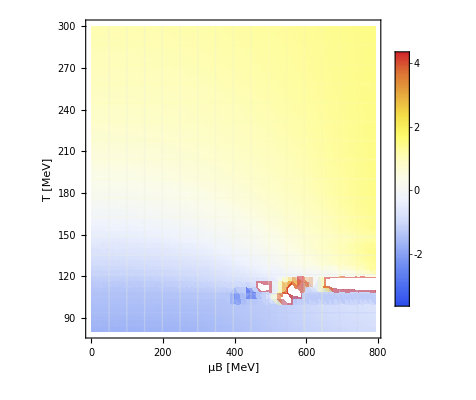

```mathematica
(*Import your data*)

indicesToAverage = Table[i,{i,1,24}];
P=Import["withpressureNsolve.mx"];

(*Flatten your data*)flatData=Flatten[P[[;;;;2,2;;;;2]],1];

(*Compute {x,y,avg z over selected indices}*)
results={#[[1]],#[[2]],Mean[Re/@#[[3,indicesToAverage]]]}&/@flatData;

(*Apply logarithm safely*)
results[[All,3]]=Log[results[[All,3]]];  (*small shift to avoid log(0)*)

(*Plot heatmap*)
ListDensityPlot[results,ColorFunction->"TemperatureMap",InterpolationOrder->1,(*or 2 for smoother*)Frame->True,FrameLabel->{"μB [MeV]","T [MeV]"},PlotLegends->Automatic,Mesh->True]
```

```mathematica
P = Import["withpressuregoal.mx"];
results = {#[[1]],#[[2]],Re[#[[3]]]}&/@P;
```

```mathematica
ListPointPlot3D[results,AxesLabel->{"μ","T","P"},PlotStyle->{Red,PointSize[Small]},Boxed->True]
```

-Graphics3D-

### Lattice data and func:

```mathematica
ClearAll[FactorApproximantComplexConstrained]
FactorApproximantComplexConstrained[coeffs_List,constraints_:{}]:=Module[{k,m,gSeries,logSeries,bList,pList,hankel,rhs,q,poly,Aroots,mRoots,vandermonde,extendedMatrix,extendedRHS,alphas,factorApprox,C,R,adjustedConstraints},(*---Step 1:series order and number of factors---*)k=Length[coeffs]-1;
m=Floor[k/2];
(*---Step 2:logarithmic series and power sums---*)gSeries=Sum[coeffs[[j+1]] x^j,{j,0,k}];
logSeries=Normal[Series[Log[gSeries],{x,0,k}]];
bList=Table[Coefficient[logSeries,x,i],{i,1,k}];
pList=Table[(-1)^(i+1) i bList[[i]],{i,1,k}];
(*---Step 3:Hankel system for Prony polynomial---*)hankel=Table[pList[[i+j-1]],{i,1,m},{j,1,m}];
rhs=-Table[pList[[m+i]],{i,1,m}];
q=LinearSolve[hankel,rhs];
(*---Step 4:Prony polynomial and numeric roots (complex allowed)---*)poly=1+Sum[q[[j]] z^j,{j,1,m}];
Aroots=1/(z/. NSolve[poly==0,z]);
mRoots=Length[Aroots];
(*---Step 5:Vandermonde system for alpha_j---*)vandermonde=Table[Aroots[[j]]^i,{i,1,mRoots},{j,1,mRoots}];
(*---Step 6:Adjust constraints length---*)adjustedConstraints=Table[{PadRight[constraints[[i,1]],mRoots],constraints[[i,2]]},{i,Length[constraints]}];
(*---Step 7:Build extended system if constraints exist---*)If[adjustedConstraints=!={},extendedMatrix=vandermonde;
extendedRHS=pList[[1;;mRoots]];
Do[{C,R}=adjustedConstraints[[i]];
extendedMatrix=Join[extendedMatrix,{C}];
extendedRHS=Join[extendedRHS,{R}],{i,Length[adjustedConstraints]}];
(*Use LeastSquares if overdetermined*)alphas=LeastSquares[extendedMatrix,extendedRHS],alphas=LinearSolve[vandermonde,pList[[1;;mRoots]]]];
(*---Step 8:Construct factor approximant---*)factorApprox=Times@@Table[(1+Aroots[[j]] x)^alphas[[j]],{j,1,mRoots}];
factorApprox]
```

```mathematica
ClearAll[FactorApproximantConstrainedComplex]
FactorApproximantConstrainedComplex[coeffs_List,constraints_:{}]:=Module[{k,m,gSeries,logSeries,bList,pList,hankel,rhs,q,poly,roots,Aroots,vandermonde,extendedMatrix,extendedRHS,alphas,factorApprox,C,R},(*---Step 1:series order and safe number of factors---*)k=Length[coeffs]-1;
m=Floor[k/2];
(*---Step 2:logarithmic series and power sums---*)gSeries=Sum[coeffs[[j+1]] x^j,{j,0,k}];
logSeries=Normal[Series[Log[gSeries],{x,0,k}]];
bList=Table[Coefficient[logSeries,x,i],{i,1,k}];
pList=Table[(-1)^(i+1) i bList[[i]],{i,1,k}];
(*---Step 3:Hankel system for q_j---*)hankel=Table[pList[[i+j-1]],{i,1,m},{j,1,m}];
rhs=-Table[pList[[m+i]],{i,1,m}];
q=LinearSolve[hankel,rhs];
(*---Step 4:Prony polynomial and numeric roots (complex allowed)---*)poly=1+Sum[q[[j]] z^j,{j,1,m}];
Aroots=1/(z/. NSolve[poly==0,z]);
mRoots=Length[Aroots];
(*---Step 5:Vandermonde system for alpha_j---*)vandermonde=Table[Aroots[[j]]^i,{i,1,mRoots},{j,1,mRoots}];
(*---Step 6:Incorporate linear constraints (optional)---*)If[constraints=!={},extendedMatrix=vandermonde;
extendedRHS=pList[[1;;mRoots]];
Do[{C,R}=constraints[[i]];
extendedMatrix=Join[extendedMatrix,{C}];
extendedRHS=Join[extendedRHS,{R}],{i,Length[constraints]}];
alphas=LinearSolve[extendedMatrix,extendedRHS],alphas=LinearSolve[vandermonde,pList[[1;;mRoots]]]];
(*---Step 7:Construct factor approximant---*)factorApprox=Times@@Table[(1+Aroots[[j]] x)^alphas[[j]],{j,1,mRoots}];
factorApprox]
```

```mathematica
ClearAll[FactorApproximantConstrained]
FactorApproximantConstrained[coeffs_List,constraints_:{}]:=Module[{k,m,gSeries,logSeries,bList,pList,hankel,rhs,q,poly,roots,realRoots,Aroots,mReal,vandermonde,extendedMatrix,extendedRHS,alphas,factorApprox,C,R},(*---Step 1:series order and safe number of factors---*)k=Length[coeffs]-1;
m=Floor[k/2];
(*---Step 2:logarithmic series and power sums---*)gSeries=Sum[coeffs[[j+1]] x^j,{j,0,k}];
logSeries=Normal[Series[Log[gSeries],{x,0,k}]];
bList=Table[Coefficient[logSeries,x,i],{i,1,k}];
pList=Table[(-1)^(i+1) i bList[[i]],{i,1,k}];
(*---Step 3:Hankel system for q_j---*)hankel=Table[pList[[i+j-1]],{i,1,m},{j,1,m}];
rhs=-Table[pList[[m+i]],{i,1,m}];
q=LinearSolve[hankel,rhs];
(*---Step 4:Prony polynomial and numeric roots---*)poly=1+Sum[q[[j]] z^j,{j,1,m}];
roots=z/. NSolve[poly==0,z];
realRoots=Select[N[roots],Im[#]==0&];
If[Length[realRoots]==0,Return[$Failed]];
Aroots=1/realRoots;
mReal=Length[Aroots];
(*---Step 5:Vandermonde system for alpha_j---*)vandermonde=Table[Aroots[[j]]^i,{i,1,mReal},{j,1,mReal}];
(*---Step 6:Incorporate linear constraints (optional)---*)If[constraints=!={},(*constraints should be a list of {C,R},where C is coeff list,R is target*)extendedMatrix=vandermonde;
extendedRHS=pList[[1;;mReal]];
Do[{C,R}=constraints[[i]];
extendedMatrix=Join[extendedMatrix,{C}];
extendedRHS=Join[extendedRHS,{R}],{i,Length[constraints]}];
alphas=LinearSolve[extendedMatrix,extendedRHS],(*No constraints*)alphas=LinearSolve[vandermonde,pList[[1;;mReal]]]];
(*---Step 7:Construct numeric factor approximant---*)factorApprox=N[Times@@Table[(1+Aroots[[j]] x)^alphas[[j]],{j,1,mReal}]];
factorApprox]
```

```mathematica
ClearAll[FactorApproximantReal]
FactorApproximantReal[coeffs_List]:=Module[{k,m,gSeries,logSeries,bList,pList,hankel,rhs,q,poly,roots,realRoots,Aroots,vandermonde,alphas,factorApprox},(*---Step 1:series order and safe number of factors---*)k=Length[coeffs]-1;
m=Floor[k/2];
(*---Step 2:logarithmic series and power sums---*)gSeries=Sum[coeffs[[j+1]] x^j,{j,0,k}];
logSeries=Normal[Series[Log[gSeries],{x,0,k}]];
bList=Table[Coefficient[logSeries,x,i],{i,1,k}];
pList=Table[(-1)^(i+1) i bList[[i]],{i,1,k}];
(*---Step 3:Hankel system for q_j---*)hankel=Table[pList[[i+j-1]],{i,1,m},{j,1,m}];
rhs=-Table[pList[[m+i]],{i,1,m}];
q=LinearSolve[hankel,rhs];
(*---Step 4:Prony polynomial and numeric roots---*)poly=1+Sum[q[[j]] z^j,{j,1,m}];
roots=z/. NSolve[poly==0,z];
(*---Keep only real roots---*)realRoots=Select[N[roots],Im[#]==0&];
If[Length[realRoots]==0,Return[$Failed,Module]];
Aroots=1/realRoots;
(*---Step 5:Vandermonde system for alpha_j---*)mReal=Length[Aroots];
vandermonde=Table[Aroots[[j]]^i,{i,1,mReal},{j,1,mReal}];
alphas=LinearSolve[vandermonde,pList[[1;;mReal]]];
(*---Step 6:construct numeric factor approximant---*)factorApprox=N[Times@@Table[(1+Aroots[[j]] x)^alphas[[j]],{j,1,mReal}]];
factorApprox]
```

```mathematica
ClearAll[FactorApproximant]
FactorApproximant[coeffs_List]:=Module[{k,m,gSeries,logSeries,bList,pList,hankel,rhs,q,poly,roots,Aroots,vandermonde,alphas,factorApprox},(*---Step 1:series order and safe number of factors---*)k=Length[coeffs]-1;(*series order*)m=Floor[k/2];(*maximum safe factors*)(*---Step 2:logarithmic series and power sums---*)gSeries=Sum[coeffs[[j+1]] x^j,{j,0,k}];
logSeries=Normal[Series[Log[gSeries],{x,0,k}]];
bList=Table[Coefficient[logSeries,x,i],{i,1,k}];
pList=Table[(-1)^(i+1) i bList[[i]],{i,1,k}];
(*---Step 3:construct Hankel system for q_j---*)hankel=Table[pList[[i+j-1]],{i,1,m},{j,1,m}];
rhs=-Table[pList[[m+i]],{i,1,m}];
q=LinearSolve[hankel,rhs];
(*---Step 4:Prony polynomial and numeric roots---*)poly=1+Sum[q[[j]] z^j,{j,1,m}];
roots=z/. NSolve[poly==0,z];
Aroots=1/N[roots];
(*---Step 5:Vandermonde system for alpha_j---*)vandermonde=Table[Aroots[[j]]^i,{i,1,m},{j,1,m}];
alphas=LinearSolve[vandermonde,pList[[1;;m]]];
(*---Step 6:construct numeric factor approximant---*)factorApprox=N[Times@@Table[(1+Aroots[[j]] x)^alphas[[j]],{j,1,m}]];
factorApprox]
```

```mathematica
(*From 1309.5258*)
Pdata = Table[{Import["WB-EoS.dat.txt","Table"][[2;;,1]][[i]],Import["WB-EoS.dat.txt","Table"][[2;;,4]][[i]]},{i,Length[Import["WB-EoS.dat.txt","Table"][[2;;,1]]]}];

AppendTo[Pdata,{0,0}]
(*From 2507.13254*)
chi2 = Import["chi2.csv"][[2;;,{1,2}]];
AppendTo[chi2,{50,0}]
chi4= Import["chi4.csv"][[2;;,{1,2}]];
AppendTo[chi4,{50,0}]
chi6 =  Import["chi6.csv"][[2;;,{1,2}]];
AppendTo[chi6,{50,0}]
chi8 =  Import["chi8.csv"][[2;;,{1,2}]];
AppendTo[chi8,{50,0}]
chi10 =  Import["chi10.csv"][[2;;,{1,2}]];
AppendTo[chi10,{50,0}]
```

{{110,0.242},{115,0.274},{120,0.308},{125,0.348},{130,0.393},{135,0.444},{140,0.501},{145,0.565},{150,0.633},{155,0.712},{160,0.798},{165,0.886},{170,0.981},{175,1.08},{180,1.18},{185,1.28},{190,1.39},{195,1.49},{200,1.58},{205,1.68},{210,1.77},{215,1.86},{220,1.95},{225,2.03},{230,2.12},{235,2.2},{240,2.27},{245,2.35},{250,2.42},{260,2.55},{270,2.68},{280,2.78},{290,2.89},{300,2.98},{310,3.07},{320,3.15},{330,3.23},{340,3.29},{350,3.36},{360,3.41},{370,3.47},{380,3.52},{390,3.56},{400,3.6},{410,3.64},{420,3.68},{430,3.71},{440,3.74},{445,3.76},{450,3.77},{455,3.79},{460,3.8},{465,3.81},{470,3.82},{475,3.84},{480,3.85},{485,3.86},{490,3.87},{495,3.88},{500,3.89},{505,3.9},{510,3.91},{0,0}}

{{99.8985,-0.000410809},{105.316,0.00109209},{110.164,0.00560333},{115.027,0.00849175},{120.088,0.0132352},{124.815,0.0199255},{130.397,0.0271542},{134.559,0.0346814},{139.784,0.0462479},{145.477,0.0616647},{149.551,0.0780511},{155.197,0.0993111},{160.016,0.121525},{164.939,0.146238},{169.816,0.170292},{174.807,0.194501},{179.688,0.215955},{184.93,0.233954},{189.677,0.250815},{194.673,0.264816},{199.753,0.277508},{204.595,0.288952},{209.559,0.297328},{219.749,0.315514},{229.853,0.326588},{240.173,0.338004},{249.686,0.34697},{259.861,0.353648},{280.198,0.365275},{299.89,0.373119},{50,0}}

{{99.8661,0.00248084},{104.98,0.00405699},{109.916,0.00639948},{114.927,0.00946704},{120.009,0.0139927},{124.685,0.0188095},{129.953,0.0260861},{135.025,0.0342994},{139.68,0.04598},{145.058,0.0590875},{150.011,0.0721791},{154.868,0.0843022},{159.848,0.0955961},{164.653,0.100045},{169.991,0.102348},{175.384,0.0972859},{180.195,0.0910596},{184.735,0.0836308},{189.708,0.0759985},{194.849,0.0691325},{199.815,0.0639869},{205.091,0.0592997},{209.646,0.0554144},{219.622,0.0493887},{230.136,0.0460162},{239.958,0.0435701},{249.851,0.0412131},{259.473,0.0398695},{279.771,0.0381724},{299.631,0.037012},{50,0}}

{{100.216,0.00226187},{105.337,0.00350831},{110.176,0.00666423},{114.906,0.00934847},{119.98,0.0143797},{124.705,0.0178139},{129.901,0.0238341},{134.93,0.0329212},{140.006,0.0403336},{144.733,0.0461717},{150.54,0.0405208},{154.691,0.0296535},{159.453,0.00119541},{164.54,-0.0320561},{170.102,-0.0704868},{174.983,-0.0851151},{179.713,-0.094826},{185.673,-0.0888751},{189.986,-0.0786502},{195.194,-0.0660689},{200.254,-0.0513764},{204.175,-0.0430723},{209.396,-0.0360985},{219.927,-0.0236599},{229.596,-0.0176843},{239.671,-0.0126985},{249.499,-0.00968534},{259.155,-0.00745416},{279.6,-0.00490025},{299.807,-0.00336315},{50,0}}

{{100.093,0.00106011},{104.872,-0.00260365},{109.983,0.00390873},{114.585,0.00530486},{119.764,0.0159796},{124.825,0.0164089},{129.615,0.0152512},{134.984,0.0032627},{139.573,0.00126822},{144.797,-0.0256181},{149.468,-0.0822221},{154.793,-0.169827},{159.59,-0.243796},{165.955,-0.201964},{170.6,-0.0431998},{173.844,0.0836529},{178.944,0.259717},{184.716,0.302759},{189.928,0.267244},{194.532,0.271849},{199.889,0.20594},{204.705,0.174623},{208.78,0.145815},{220.111,0.0800108},{229.11,0.0518151},{239.233,0.0318617},{249.585,0.0234979},{259.227,0.0185334},{279.15,0.0105078},{298.944,0.00628475},{50,0}}

{{100.706,-0.0128046},{104.884,-0.119683},{109.96,-0.0868061},{114.784,-0.111839},{119.915,-0.0445854},{125.052,-0.0873252},{129.584,-0.0204758},{135.232,-0.0967844},{139.813,-0.144138},{145.227,-0.675242},{149.762,-0.929661},{155.057,-0.259841},{160.07,0.712098},{165.028,1.53627},{169.861,2.009},{174.873,1.11856},{180.139,-0.0872675},{184.681,-0.874001},{189.442,-1.29073},{195.011,-1.31645},{199.919,-1.11175},{204.962,-0.932949},{209.574,-0.709387},{219.804,-0.395789},{229.883,-0.306215},{239.439,-0.184571},{249.353,-0.149214},{259.773,-0.0715789},{279.651,-0.0375487},{299.79,-0.0351262},{50,0}}

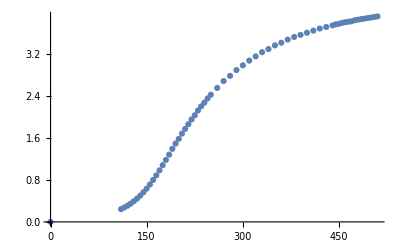

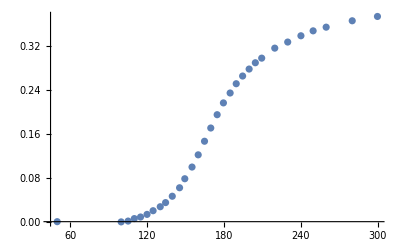

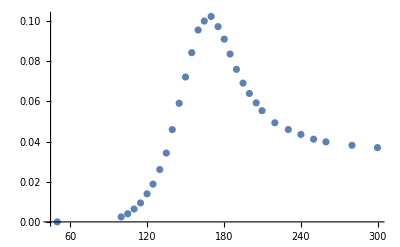

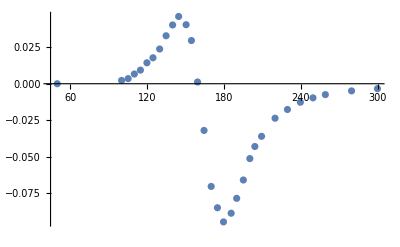

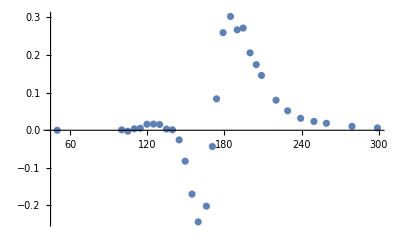

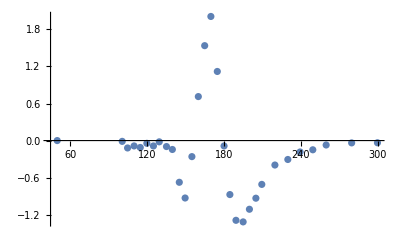

```mathematica
ListPlot[Pdata]
ListPlot[chi2]
ListPlot[chi4]
ListPlot[chi6]
ListPlot[chi8]
ListPlot[chi10]
```